# Cuaderno de Prácticas

## Análisis y métodos numéricos

## Grado en Ingeniería Informática

## CURSO 2024/25

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : 2
Grupo de prácticas :

## Práctica 7

Integrales

```mathematica
f[x_]:=x^2+2
```

```mathematica
∫f[x]ⅆx
```

2 x+x^3/3

```mathematica
Integrate[f[x],x]
```

2 x+x^3/3

```mathematica
∫Log[Cos[x+3]]ⅆx
```

1/2 ⅈ (3+x)^2-(3+x) Log[1+ⅇ^(2 ⅈ (3+x))]+(3+x) Log[Cos[3+x]]+1/2 ⅈ PolyLog[2,-ⅇ^(2 ⅈ (3+x))]

```mathematica
∫Log[Cos[x+3]]ⅆx //Simplify
```

1/2 ((3+x) (ⅈ (3+x)-2 Log[1+ⅇ^(2 ⅈ (3+x))]+2 Log[Cos[3+x]])+ⅈ PolyLog[2,-ⅇ^(2 ⅈ (3+x))])

```mathematica
∫_0^2 f[x]ⅆx
```

20/3

El Apart divide en funciones simples:

```mathematica
Apart[(3 x^2+3)/(x^3-x)]
```

3/(-1+x)-3/x+3/(1+x)

Repaso 2
Sea la función f(x)=x^2+2 en el intervalo [1,3]

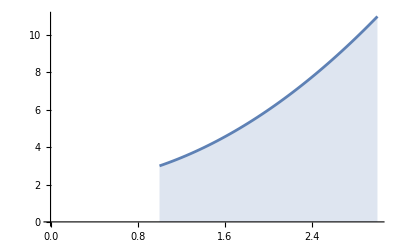

```mathematica
Plot[x^2+2,{x,1,3},AxesOrigin->{0,0}, Filling->Axis]
```

Se puede aproximar por la media de los valores en una partición del intervalo . Podemos hacer n subintervalos de anchura Δ x .

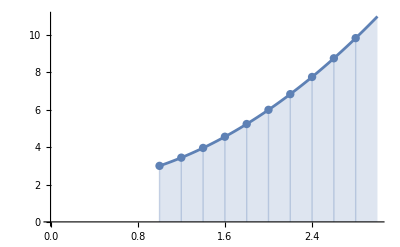

```mathematica
Show[Plot[x^2+2,{x,1,3},AxesOrigin->{0,0}, Filling->Axis],ListPlot[Table[{1+i/5,(1+i/5)^2+2},{i,0,9}], PlotStyle->PointSize[0.015], Filling->Axis]]
```